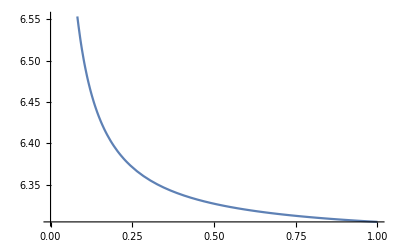

```mathematica
(*Function definitions*)
ck[k_]:=(4-k)*(5-k)^((-(5-k))/(4-k));
xsq[r_,y_,thv_,phi_,k_]:=y^2*Tan[thv]^2+2*r*y*Tan[thv]*Cos[phi]+r^2;
chi[x_,y_,k_]:=(y-ck[k]*x)/y^(5-k);

(*Constant definitions*)
TORAD=π/180.;
Y=0.2;
R0=0.1;
THV=6.0*TORAD;
PHI=0.0;
K=0.0;

(*Solve for r'*)
(*rFunc[r0_,y_,thv_,phi_,k_]:=Solve[chi[xsq[r,y,thv,phi,k],y,k]==chi[xsq[r0,y,thv,0.0,k],y,k],r];
r[r0_,y_,thv_,phi_,k_]:=x/.rFunc[[1]]
Solve[chi[xsq[r,y,thv,phi,k],y,k]==1,r]//FullSimplify;*)
rPrimeVals=Solve[r^2+2*r*y*Tan[thv]*Cos[phi]==r0^2+2*y*r0*Tan[thv],r];
rPrimePlus[rVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeVals[[1]]/.{r0->rVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
rPrimeMinus[rVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeVals[[2]]/.{r0->rVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
rPrime[rVal_,yVal_,tVal_,pVal_,kVal_]:=rPrimeVals[[2]]/.{r0->rVal,y->yVal,thv->tVal,phi->pVal,k->kVal};
PhiIntegrand[rVal_,yVal_,tVal_,pVal_,kVal_]:=(r/rVal)^2/.rPrime[rVal,yVal,tVal,pVal,kVal];
PhiInt[rVal_,yVal_,tVal_,kVal_]:=NIntegrate[PhiIntegrand[rVal,yVal,tVal,phi,kVal],{phi,0,2*π}];
Plot[PhiInt[r0,0.1,1.0*TORAD,0.0],{r0,0.0,1.0}]

(*Plotting*)
Manipulate[Plot[PhiInt[r0,y,thv*TORAD,0.0],{r0,0.0,1.0}],{y,0.0,1.0,0.1},{thv,0.0,10.0,1.0}]
Manipulate[Plot[PhiIntegrand[R0,Y,THV,phi,K],{phi,0,2*π}],{THV,0.0,15.0*TORAD,0.01*TORAD}]
Manipulate[Plot[PhiInt[r0,Y,thv,K],{r0,0.0,0.5}],{thv,0.0,15.0*TORAD,0.01*TORAD}];
```